## Import

```mathematica
fn =FileNames[All, "/Users/erichegonzales/Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/cbball_data/01-19-23"][[;;-3]];
```

```mathematica
fn2 =FileNames[All, "/Users/erichegonzales/Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/cbball_data/01-19-23"][[;;-3]];
```

```mathematica
testGames = Import[#, "Dataset", "HeaderLines"->1]&/@ fn;
```

```mathematica
testCloseGames = Select[testGames, #[[-1, "score_diff"]]<10&];
```

## Processing

```mathematica
getPossStatuses[game_]:=Module[{i, possStatuses,possStatus, row, curr, homeTeam, awayTeam, currTeam},
i = 1;
possStatuses = {};
row = game[[1]];
homeTeam = row[["home"]];
awayTeam = row[["away"]];
While[i<=Length[game],
curr = row[["possession_before"]];
If[curr == homeTeam, currTeam = "home", currTeam = "away"];
possStatus=currTeam<>"Empty";
While[row[["possession_before"]] == curr, 
If[row[["shot_outcome"]] == "made", possStatus = currTeam<>"Score"];
i += 1;
row = game[[i, All]];
];
AppendTo[possStatuses, possStatus]
];
possStatuses
]
```

```mathematica
gamePossStatuses = getPossStatuses/@testCloseGames;
```

```mathematica
metadata = <|"n"->0,"nHome"->0, "nAway"->0,"homeCount"->0,"awayCount"->0,"homeECount"->0,"awayECount"->0,"pHome"->0,"pAway"->0, "pHEmpty"->0, "pAEmpty"->0 |>;
```

```mathematica
metadata["n"] = Length[Flatten[gamePossStatuses]];
metadata["nHome"] =Length[Select[Flatten[gamePossStatuses], StringContainsQ[#, "home"]&]];
metadata["nAway"] =Length[Select[Flatten[gamePossStatuses], StringContainsQ[#, "away"]&]];
metadata["homeCount"] = Count[gamePossStatuses, "homeScore", 2] ;
metadata["awayCount"] = Count[gamePossStatuses, "awayScore", 2] ;
metadata["homeECount"] = Count[gamePossStatuses, "homeEmpty", 2] ;
metadata["awayECount"] = Count[gamePossStatuses, "awayEmpty", 2] ;
metadata["pHome"] = metadata["homeCount"] / metadata["nHome"];
metadata["pAway"] = metadata["awayCount"] / metadata["nAway"];
metadata["pHEmpty"] = metadata["homeECount"] / metadata["nHome"];
metadata["pAEmpty"] = metadata["awayECount"] / metadata["nAway"];
metadata
```

<|n→6703,nHome→3347,nAway→3356,homeCount→1548,awayCount→1665,homeECount→1799,awayECount→1691,pHome→1548/3347,pAway→1665/3356,pHEmpty→1799/3347,pAEmpty→1691/3356|>

```mathematica
chooseHome[]:= RandomChoice[{metadata["pHome"], metadata["pHEmpty"]}->{1, 0}]
chooseAway[]:= RandomChoice[{metadata["pAway"], metadata["pAEmpty"]}->{-1, 0}]
simPoss[status_]:= If[StringContainsQ[status, "home"], chooseHome[], chooseAway[]]
```

```mathematica
simPossStatuses = Map[simPoss, gamePossStatuses, {2}];
```

```mathematica
simposstable = Table[Flatten[Map[simPoss, gamePossStatuses, {2}]], 10];
```

```mathematica
possStatuses10 = Map[If[# == "homeScore", 1, If [# == "awayScore", -1, 0]]&, Flatten[gamePossStatuses]];
```

```mathematica
diffsReal = Differences[Accumulate[possStatuses10], 1, 10];
```

```mathematica
diffsSim = Differences[Accumulate[#], 1, 10]&/@ simposstable
```

```mathematica
histdata = Prepend[Sort[Tally[#]]&/@ diffsSim, Sort[Tally[diffsReal]]];
histrow = Flatten@histdata[[All, All, 1]];
histcol = Flatten@histdata[[All, All, 2]];
diffidx = Flatten@MapIndexed[Table[First@#2, Length@#1]&, histdata];
histtable = Prepend[Transpose[{diffidx, histrow, histcol }], {"diff_idx", "hist_row", "hist_col"}] ;
```

## Visualization

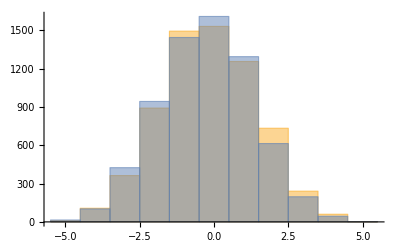

```mathematica
Histogram[{diffsReal, diffsSim}]
```

## Export

```mathematica
RangeCycle[total_,range_]:=Mod[Range[total]-1,range]+1
```

```mathematica
numpartition[total_,range_]:=Flatten[Table[i,{i,Ceiling[total/range]}],1][[1;;total]]
```

```mathematica
outdir ="Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/output/01-19-23/";
```

```mathematica
gameids = MapIndexed[Table[First@#2, Length@#1]&, gamePossStatuses];
grididxs = PadRight[Flatten[Table[{i, j}, {i, 1, 9}, {j, 1, 6}], 1], 50];
rowidxs = MapThread[Table[#2[[1]], Length@#1]&, {gamePossStatuses, grididxs}];
colidxs = MapThread[Table[#2[[2]], Length@#1]&, {gamePossStatuses, grididxs}];
```

```mathematica
playidxs = Range[Length@#]&/@ gamePossStatuses;
```

```mathematica
pretab =  Join[{Flatten@gameids,Flatten@rowidxs,Flatten@colidxs,Range[Length@possStatuses10],Flatten@playidxs,possStatuses10,Flatten@simPossStatuses}, simposstable]
```

```mathematica
simnames = Table["S"<>ToString@i, {i,1, 10}];
```

```mathematica
posstable  =
Prepend[Transpose[pretab],
 Join[
{"game_id","row_idx", "col_idx", "total_idx","play_idx", "poss_status", "sim_pos_status"}, 
simnames]
]
```

```mathematica
Export[outdir<>"posstable.csv", posstable]
```

Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/output/01-19-23/posstable.csv

```mathematica
Export["Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/output/metadata.csv", Dataset[{metadata}]]
```

Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/metadata.csv

```mathematica
simtable = Transpose[simposstable];
```

```mathematica
Export[outdir<>"simtable.csv", simtable]
```

Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/output/01-19-23/simtable.csv

```mathematica
Export[outdir<>"histtable.csv", histtable]
```

Projects/Wolfram/Probability Research/GameOfRunsCBBall-08-11-24/output/01-19-23/histtable.csv

## Querying Database

```mathematica
testCloseGames[[1]][1, Keys] //Normal
```

{game_id,date,home,away,play_id,half,time_remaining_half,secs_remaining,secs_remaining_absolute,description,action_team,home_score,away_score,score_diff,play_length,scoring_play,foul,win_prob,naive_win_prob,home_time_out_remaining,away_time_out_remaining,home_favored_by,total_line,referees,arena_location,arena,capacity,attendance,shot_x,shot_y,shot_team,shot_outcome,shooter,assist,three_pt,free_throw,possession_before,possession_after,wrong_time}

```mathematica
testCloseGames[[1]][All, {"home", "away", "action_team", "description", "shot_outcome", "possession_before"}]
```

```mathematica
Normal[#[Select[#[["action_team"]] == "away"&]][Count["made"], "shot_outcome"]]&/@ testCloseGames // Total
```

1985

```mathematica
#[1, ]
```

```mathematica
Normal@#[1, {"home", "away"}]&/@ testCloseGames
```

{<|home→Austin Peay,away→Bellarmine|>,<|home→Florida Gulf Coast,away→Jacksonville State|>,<|home→Jacksonville,away→Liberty|>,<|home→North Florida,away→Queens University|>,<|home→Stetson,away→Kennesaw State|>,<|home→Northern Colorado,away→Eastern Washington|>,<|home→Northern Arizona,away→Idaho|>,<|home→Idaho State,away→Sacramento State|>,<|home→UC Davis,away→UC Riverside|>,<|home→Long Beach State,away→Cal State Fullerton|>,<|home→UC Irvine,away→Hawai'i|>,<|home→Cal Poly,away→UC San Diego|>,<|home→North Carolina A&T,away→Towson|>,<|home→Drexel,away→Hampton|>,<|home→Monmouth,away→Charleston|>,<|home→Stony Brook,away→Northeastern|>,<|home→Northern Kentucky,away→Cleveland State|>,<|home→Wright State,away→Purdue Fort Wayne|>,<|home→IUPUI,away→Oakland|>,<|home→Green Bay,away→Youngstown State|>,<|home→Lindenwood,away→Southern Indiana|>,<|home→Little Rock,away→Tennessee Tech|>,<|home→Tennessee State,away→Eastern Illinois|>,<|home→SIU Edwardsville,away→Morehead State|>,<|home→Southeast Missouri State,away→UT Martin|>,<|home→North Dakota State,away→Oral Roberts|>,<|home→Coastal Carolina,away→Appalachian State|>,<|home→Georgia Southern,away→UL Monroe|>,<|home→Troy,away→James Madison|>,<|home→Texas State,away→Marshall|>,<|home→Arkansas State,away→Louisiana|>,<|home→Southern Miss,away→South Alabama|>,<|home→Santa Clara,away→BYU|>,<|home→Portland,away→San Diego|>,<|home→Gonzaga,away→Loyola Marymount|>,<|home→Pepperdine,away→Saint Mary's|>,<|home→VMI,away→Mercer|>,<|home→Sam Houston,away→Stephen F. Austin|>,<|home→Illinois,away→Indiana|>,<|home→Maryland,away→Michigan|>,<|home→Minnesota,away→Purdue|>,<|home→Houston Christian,away→Incarnate Word|>,<|home→Lamar,away→Texas A&M-Corpus Christi|>,<|home→New Orleans,away→Texas A&M-Commerce|>,<|home→Nicholls,away→McNeese|>,<|home→SE Louisiana,away→Northwestern State|>,<|home→Middle Tennessee,away→Charlotte|>,<|home→North Texas,away→Rice|>,<|home→UTSA,away→Florida Atlantic|>,<|home→Colorado,away→Washington|>}

## Scratchpad

```mathematica
Mod[8, 6]
```

2